I)
The fixed points are written in order.

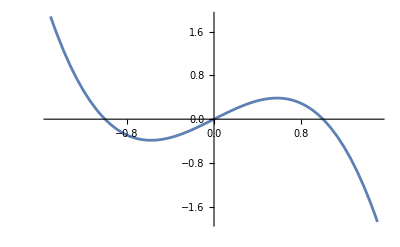

{{x→-1},{x→0},{x→1}}

```mathematica
Plot[x-x^3,{x,-1.5,1.5}]
Solve[x-x^3==0,x]
```

Stable, Unstable, Stable.

Method 2
Check x^(..) for minima and maxima
If x^(..) >0 : unstable
If x^(..) <0 : stable

II)
\[MathematicaIcon]

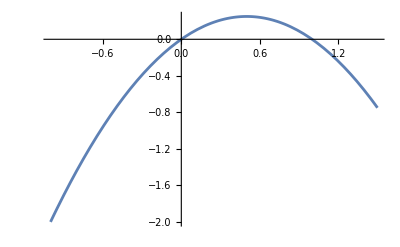

{{x→0.},{x→1.}}

```mathematica
Plot[x(1-x),{x,-1,1.5}]
Solve[x(1-x)==0,x]//N
```

Unstable, Stable.

\[MathematicaIcon]

```mathematica
Eq = Manipulate[Plot[r-x-x^3,{x,-5,2}],{r,-10,10}]
Manipulate[Solve[r-x-x^3==0,x,Reals],{r,-10,10}]
```

r=x+x^3 is always a stable fixed point.

\[MathematicaIcon]

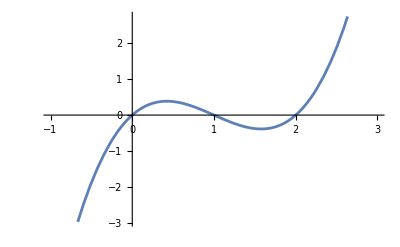

```mathematica
Plot[x(x-1) (x-2),{x,-1,3}]
```

```mathematica
Solve[x(x-1) (x-2)==0,x]
```

{{x→0},{x→1},{x→2}}

Unstable, Stable, Unstable

\[MathematicaIcon]

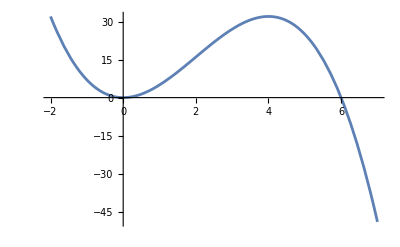

{{x→0},{x→0},{x→6}}

```mathematica
Plot[x^2(6−x),{x,-2,7}]
Solve[x^2(6−x)==0,x]
```

Semi-stable, Semi-stable, Stable

\[MathematicaIcon]

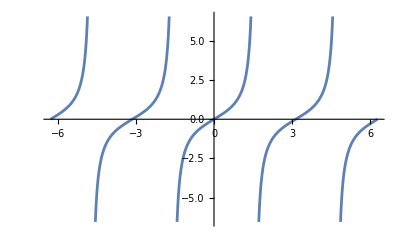

{{x→ConditionalExpression[π C[1], C[1]∈ℤ]}}

```mathematica
Plot[Tan[x],{x,-2Pi,2Pi}]
Solve[Tan[x]==0,x]
```

All unstable points

\[MathematicaIcon]

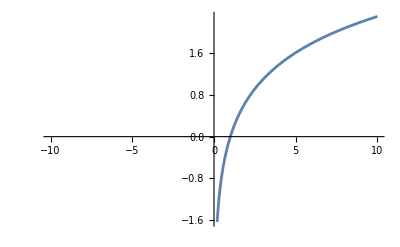

{{x→1}}

```mathematica
Plot[Log[x],{x,-10,10}]
Solve[Log[x]==0,x]
```

## Unstable equilibrium. III) Gompertz law Change in a does not affect the equilibrium points

```mathematica
Manipulate[Plot[-a n Log[b n],{n,0,2}],{a,1,10},{b,1,10}]
Manipulate[Solve[-a n Log[b n]==0,n],{a,1,10},{b,1,10}]
```

>SYNC
>Apart from the following, n=0 is an UNSTABLE fixed point. The stable equilibrium point:

For N(t) we integrate Ṅ

IV) Divergence and Curl

(a)

```mathematica
Div[{x y, y z, 0},{x,y,z}]
Curl[{x y, y z, 0},{x,y,z}]
VectorPlot3D[{x y, y z, 0},{x,-4,4},{y,-1,1},{z,-10,10},PlotLegends->Automatic,AxesLabel->{"x","y","z"}]
```

y+z

{-y,0,-x}

-Graphics3D-

(b)The curl and divergence are the same [Fascinating!]

2 x-2 y

2 x-2 y

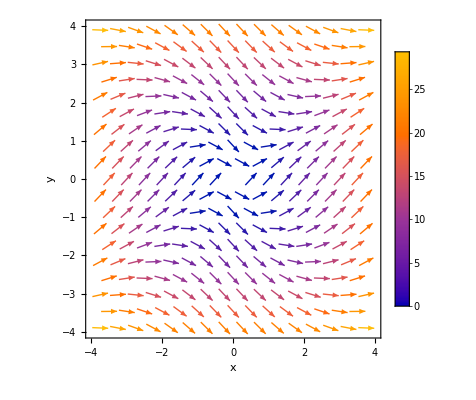

```mathematica
Div[{x^2+y^2, x^2-y^2},{x,y}]
Curl[{x^2+y^2, x^2-y^2},{x,y}]
VectorPlot[{x^2+y^2, x^2-y^2},{x,-4,4},{y,-4,4},PlotLegends->Automatic,AxesLabel->{"x","y"}]
```

## V) Let μ_o/(4 π)=1

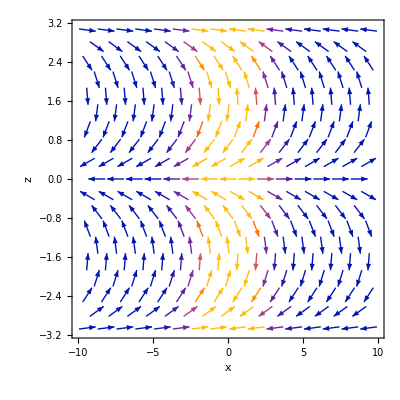

```mathematica
VectorPlot[{1/r^3 2 Cos[θ],1/r^3 Sin[θ]},{r,-10,10},{θ,-Pi,Pi},AxesLabel->{"x","z"}]
```

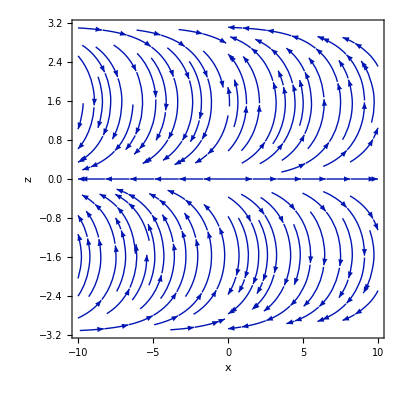

```mathematica
StreamPlot[{1/r^3 2 Cos[θ],1/r^3 Sin[θ]},{r,-10,10},{θ,-Pi,Pi},AxesLabel->{"x","z"}]
```

VI)

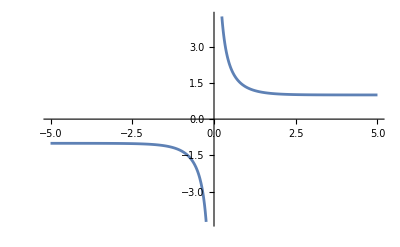

```mathematica
Plot[Coth[x],{x,-5,5}]
```

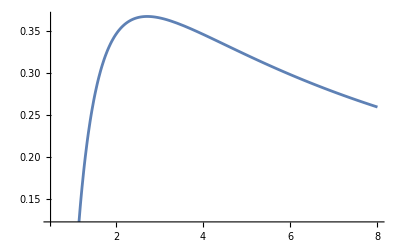

```mathematica
Plot[Log[x]/x,{x,0.5,8}]
```

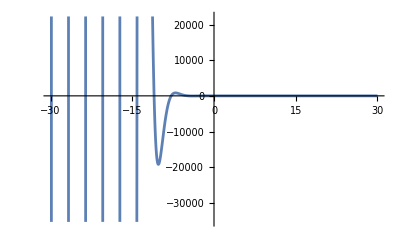

```mathematica
Plot[Exp[-x] Cos[x],{x,-30,30}]
```

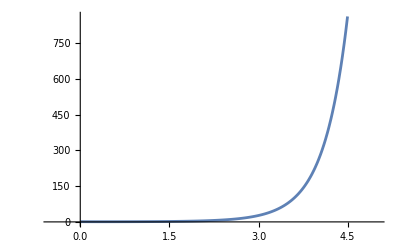

```mathematica
Plot[x^x,{x,-0.5,5}]
```

```mathematica
Plot[1/x^12-1/x^6,{x,-8,8},PlotRange->All]
```

-Graphics-